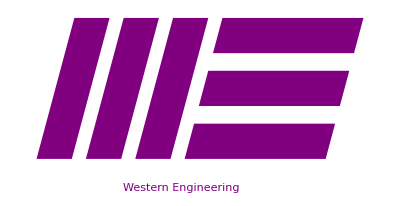

```mathematica
xStep = 1.4;
barLength = 4;
barWidth = 1;
vb0 = {Purple, Rectangle[{xStep*0, 0},{xStep*0+barWidth, barLength}]};
vb1 = {Purple, Rectangle[{xStep*1, 0},{xStep*1+barWidth, barLength}]};
vb2 = {Purple, Rectangle[{xStep*2, 0},{xStep*2+barWidth, barLength}]};
hb0 = {Purple, Rectangle[{xStep*3, 0}, {xStep*3+barLength, barWidth}]};
hb1 = {Purple, Rectangle[{xStep*3, (barLength-barWidth)/2}, {xStep*3+barLength, (barLength+barWidth)/2}]};
hb2 = {Purple, Rectangle[{xStep*3, barLength-barWidth}, {xStep*3+barLength, barLength}]};
Logo = {GeometricTransformation[Join[vb0,vb1,vb2, hb0, hb1, hb2], ShearingTransform[15 Degree, {1,0}, {0,1}]]};
WE = {Purple, Text[Style["Western Engineering", Large],{(xStep*3+barLength)/2, -.8}]};
Graphics[Join[Logo, WE]]
```